## Manipulate[ ] powers to consider:

### Appearance, Control Placement, dropdown boxes, buttons, deafult values, time steps, ...

```mathematica
Options[Manipulate][[All]]
```

{Alignment→Automatic,AppearanceElements→Automatic,AutoAction→False,AutorunSequencing→Automatic,BaselinePosition→Automatic,BaseStyle→{},Bookmarks→{},ContentSize→Automatic,ContinuousAction→Automatic,ControlAlignment→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,ControlPlacement→Automatic,ControlType→Automatic,DefaultBaseStyle→Manipulate,DefaultLabelStyle→ManipulateLabel,Deinitialization:>None,Deployed→False,Evaluator→Automatic,Frame→False,FrameLabel→None,FrameMargins→Automatic,ImageMargins→0,Initialization:>None,InterpolationOrder→Automatic,LabelStyle→{},LocalizeVariables→True,Method→{},Paneled→True,PreserveImageOptions→True,RotateLabel→False,SaveDefinitions→False,ShrinkingDelay→0,SynchronousInitialization→True,SynchronousUpdating→Automatic,TouchscreenAutoZoom→False,TouchscreenControlPlacement→Automatic,TrackedSymbols→Full,UnsavedVariables:>None,UntrackedVariables:>None}

## Manipulate allows you to dynamically change variables in a visual way

```mathematica
ClearAll["Global`*"]

Manipulate[
Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},PlotRange->2],
{n1,1,20}, (*min=1, max=20*)
{n2,1,20,3} (*note step size, avoid ugly behavior?*)
]
```

## You can quickly build interactive tools!

```mathematica
ClearAll["Global`*"]

Manipulate[
g[x_]:=a x^2+b x+c;
Plot[g[y],{y,d,e},PlotStyle->Dashing[{.01}],PlotRange->99,ImageSize->{500,500}],
{a,-99,99,1},
{b,-99,99,1},
{c,-99,99,1},
{d,-30,0,1},
{e,0.01,30,1}
]
```

## Make the tools better:

### Set slider steps, default start values, output variable amount, improved descriptive titles, ...

```mathematica
ClearAll["Global`*"]

Manipulate[
g[x_]:=a x^2+b x+c;
Plot[g[y],{y,d,e},PlotStyle->Dashing[{.01}],PlotRange->99,ImageSize->{400,400}],
{a,-99,99,2}, (*Set slider's steps*)
{{b,19},-99,99,1}, (*Set default start values*)
{{c,-15},-99,99,1,Appearance->"Labeled"}, (*"label the slider"*)
{{d,-8,"L endpoint"},-30,0,1,Appearance->"Labeled"}, (*Label (display) the slider's value*)
{{e,5,"R endpoint"},0.01,30,1,Appearance->"Labeled"}]
```

## Change the placement of sliders for maximum screen real estate

```mathematica
Manipulate[
g[x_]:=a x^2+b x+c;
Plot[g[y],{y,d,e},PlotStyle->Dashing[{.01}],PlotRange->99,ImageSize->{400,400}],
{{a,0,"integer a"},-99,99,1, Appearance->"Labeled"},
{{b,19,"integer b"},-99,99,1,Appearance->"Labeled"},
{{c,-15,"integer c"},-99,99,1,Appearance->"Labeled"},
{{d,-5,"L endpoint"},-30,0,1,Appearance->"Labeled"}, (*Center the axis*)
{{e,5,"R endpoint"},0.01,30,1,Appearance->"Labeled"},
TrackedSymbols->True,ControlPlacement->Right](*Change position of slider layout*)
```

## You can also make dropdown selecters

```mathematica
ClearAll["Global`*"]

Manipulate[
Plot[Sin[n1 *x]/a+b*Sin[n2* x],{x,0,2 Pi},Filling->filling,PlotRange->2],
{n1,1,20, Appearance->"Labeled"},
{n2,1,20, Appearance->"Labeled"},
{a,1,20, Appearance->"Labeled"},
{b,1,10, Appearance->"Labeled"},
{filling,{None,Axis,Top,Bottom,Automatic,1,0.5,0,-0.5,-1}},(*<-- Here!*)
ControlPlacement->Right 
]
```

## Consider adding manipulate to difficult to visualize functions

```mathematica
ClearAll["Global`*"]

Manipulate[
pl[n,m],
{n, 0, Pi},
{m, 0, Pi}
]
(*Make more complicated manipulatations a function, painlessly introduce manipulate*)
pl[n_,m_]:=Plot3D[Sin[n*x]Cos[m*y], {x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

## Behavior of systems may not be obvious while dynamic visuals add insight!

### Try using the play button - Located under the “+“ on the output.

```mathematica
ClearAll["Global`*"]

Manipulate[
ppm[preyGrowth,preyDeath, predGrowth, predDeath],
{preyGrowth, -2, 2, Appearance->"Labeled"},
{preyDeath, -2, 2, Appearance->"Labeled"},
{predGrowth, -2, 2, Appearance->"Labeled"},
{predDeath, -2, 2, Appearance->"Labeled"},
ControlPlacement->Right 
]

ppm[preyGrowth0_,preyLoss0_, predGrowth0_, predLoss0_]:=
Module[{
preyGrowth=preyGrowth0,
preyLoss=preyLoss0,
predGrowth=predGrowth0,
predLoss=predLoss0 },
f[x_,y_]=preyGrowth-x^2+y-preyLoss;
g[x_,y_]=predGrowth+x-y^2-predLoss;

sp=StreamPlot[{f[x,y],g[x,y]},{x,-1,4},{y,-1,4}]
]
```

## You can make some neat examples of systems and behavior

```mathematica
(*
Taken from: http://reference.wolfram.com/mathematica/ref/StreamPlot.html
*)
ClearAll["Global`*"]
f1[y_]:=y;
g1[x_,y_]:=-Sin[x]-.25 y

splot = StreamPlot[{f1[y],g1[x,y]},{x,-4,4},{y,-3,3}];
Manipulate[Show[splot,
ParametricPlot[Evaluate[First[{x[t],y[t]} /. NDSolve[{x'[t]==f1[y[t]],y'[t]==g1[x[t],y[t]],Thread[{x[0],y[0]}==point]},{x,y},{t,0,T}]]],{t,0,T},PlotStyle->Red]],
{{T,10},1,100},{{point,{1,0}},Locator}, SaveDefinitions->True]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Show::gcomb: Could not combine the graphics objects in splot, GraphicsBox[List[], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 0.`], List[0.`, 0.`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]].

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Show::gcomb: Could not combine the graphics objects in splot, GraphicsBox[List[], List[Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 0.`], List[0.`, 0.`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]].

## Use Manipulate as a method to teach (or study)

```mathematica
ClearAll["Global`*"]

Manipulate[Row[{Text["m"]==MatrixForm[m],StreamPlot[Evaluate[m.{x,y}],{x,-50,50},{y,-50,50}, StreamScale->Large, StreamColorFunction->"Rainbow"
]}],
{{m,({{1, 0}, {0, 2}})}, { (*Deafult value, quickly show others*)
({{1, 0}, {0, 2}})->"Nodal source",
({{1, 1}, {0, 1}})->"Degenerate source",
({{0, 1}, {-1, 1}})->"Spiral source",
({{-1, 0}, {0, -2}})->"Nodal sink",
({{-1, 1}, {0, -1}})->"Degenerate sink",
({{0, 1}, {-1, -1}})->"Spiral sink",
({{0, 1}, {-1, 0}})->"Center",
({{1, 0}, {0, -2}})->"Saddle"}}]
```

## Lots of ways to maximize your visual experience in different topics

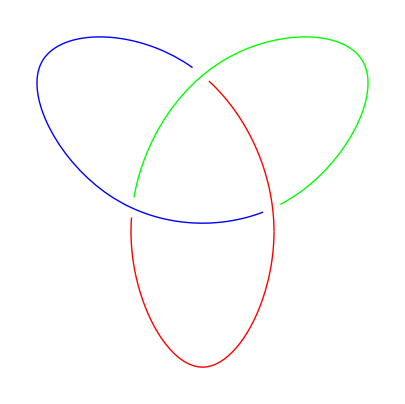

```mathematica
(*Introduction to knots*)
ClearAll["Global`*"]
Graphics[Transpose[{{Red,Blue,Green,Red},KnotData["Trefoil", "KnotDiagramData"]}]]
```

```mathematica
(*Vary certain knots for more exposure*)
Manipulate[
knot[n],
{n, 10, 20,1}
]

knot[y_]:=Graphics[Transpose[{Table[RGBColor @@ RandomReal[{0,1},3],{Length[#]}], #}]]& @KnotData[{"TorusKnot",{7,y}},"KnotDiagramData"]
```

```mathematica
(*More of the same but in 3D*)
ClearAll["Global`*"]
coloredknot[knot_, colorFunction_] :=
With[{a = First @ KnotData[knot,"ImageData"]},
Graphics3D[GraphicsComplex[a[[1]], a[[2]],a[[3]], VertexColors -> colorFunction @@@a[[1]]], Boxed -> False]]


Manipulate[
knot2[n],
{n, 2, 15,1}
]

knot2[x_]:=coloredknot[{"TorusKnot",{3,x}},Hue[Sin[#1]]&]
```

```mathematica
(*practice shape naming*)
ClearAll["Global`*"]

Manipulate[Column[{PolyhedronData[g],PolyhedronData[g,p]}],
{g,PolyhedronData[All]},
{p,Complement@@PolyhedronData/@{"Properties","Classes"}}]
```

## Last - Add buttons to perform other behavior

```mathematica
(*Generating random numbers*)
ClearAll["Global`*"]
Manipulate[x,{{x,"NICE!"},Button["random",x=RandomChoice[{"Cameron","A+","Great Presentation"},3]]&}]
```